## Absorbing Cylinder in KG

This notebook is associated with chapter 4 of the Master Thesis “Analogue Binaries and Superradiance”.

### Clean Variables

In case you run into any of Mathematica problems, just clean all variables and go at it again

```mathematica
(*Clear all variables *)
ClearAll["Global`*"]
```

### Eigenfunction

As pointed out in the document, we wish to calculate the eigenfrequencies w given by the equation (EQUATION). The parameters we have are:

	m : Azimuthal number
	Ω: Cylinder rotation speed 
	R0: Outer cavity radius (in units of the inner cylinder radius)
	α : Absorption Parameter
	
The function presented in the main document has been obtained by the “pencil and paper” method, but It could as well have been obtained by solving the KG equation in Mathematica. We shall pursue this last method in the following section.

We begin by defining our quantities:

```mathematica
(* ND is the number of spacetime dimensions in the problem. *)
(* Has to be in accord with metric;                         *)
(* g is covariant metric                                    *)

ND=3;

(*Covariant metric in polar coordinates*)
g=DiagonalMatrix[{-1,1,r^2}];

(*A is the contravariant metric*)
A=Inverse[g];

(*Coordinates*)
X={t,r,phi};

(*Γ are the metric connections (Christoffel symbols) the first index is up the next two are down*)
Γ=Table[Sum[1/2A[[c,d]]*(D[g[[b,d]],X[[a]]]+D[g[[a,d]],X[[b]]]-D[g[[a,b]],X[[d]]]),{d,1,ND}],{c,1,ND},{a,1,ND},{b,1,ND}];

(*Riemann Tensor with all indices down: Rie[[a,b,c,d]]*)Rie=Table[Sum[g[[f,a]](D[Γ[[f,b,d]],X[[c]]]-D[Γ[[f,b,c]],X[[d]]]+Sum[Γ[[e,b,d]]Γ[[f,e,c]],{e,1,ND}]-Sum[Γ[[e,b,c]]Γ[[f,e,d]],{e,1,ND}]),{f,1,ND}],{a,1,ND},{b,1,ND},{c,1,ND},{d,1,ND}];

(*Covariant Ricci tensor (indices down)*)Riccit=Table[Sum[D[Γ[[a,b,d]],X[[a]]]-D[Γ[[a,b,a]],X[[d]]]+Sum[Γ[[e,b,d]]Γ[[a,e,a]],{e,1,ND}]-Sum[Γ[[e,b,a]]Γ[[a,e,d]],{e,1,ND}],{a,1,ND}],{b,1,ND},{d,1,ND}];

(*Ricci Scalar*)
Riccie=Simplify[Sum[A[[a,b]]Riccit[[a,b]],{a,1,ND},{b,1,ND}]];
```

The ansatz used can now be substituted in the KG equation:

```mathematica
(* Function Decomposition*)
Psi=PSI[r]*Exp[-I*wt*t+I*m*phi];

(*KG Equation*)
KG1=1/Sqrt[-Det[g]]Sum[D[Sqrt[-Det[g]]*A[[a,b]]*D[Psi,X[[a]]],X[[b]]],{a,1,ND},{b,1,ND}]-alpha*(D[Psi,t]- Ω*D[Psi,phi]);

(*Simplified Version*)
FullSimplify[KG1]
```

(ⅇ^(ⅈ (m phi-t wt)) ((-m^2+r^2 wt (ⅈ alpha+wt)+ⅈ alpha m r^2 Ω) PSI[r]+r (PSI'[r]+r PSI''[r])))/r^2

and Mathematica can kindly match the boundary conditions

```mathematica
(*  
	Interior Solution ; 
	must be regular at r = 0 -> No BesseY
*)
solint=BesselJ[m,r  √(ⅈ alpha*w+w^2- ⅈ * alpha * m * Omega)] C1;

(*Exterior Solution -> Bessel Sum*)
solext=BesselJ[m,r √-w √-w] C3+BesselY[m,r √-w √-w] C4;

(*Derivatives of solutions*)
dsolint = D[solint,r];
dsolext = D[solext,r];

(*Solution Matching at inner Radius*)
solint…at…R1 = solint/.r-> R1;
solext…at…R1 = solext/.r-> R1;

dsolint…at…R1 = dsolint/.r-> R1;
dsolext…at…R1 = dsolext/.r-> R1;

(*Find solution*)
parsol=Solve[
			{solint…at…R1==solext…at…R1,
			dsolint…at…R1 == dsolext…at…R1},
			{C3,C4}
	][[1]]//Simplify;

(*Substitute back at outer solution*)
solext…at…R2 = Simplify[solext/.r-> R2/.parsol/.C1-> 1];
```

The function whose zeros we need to find is then:

```mathematica
(*Define Response Function*)
Gw[iw_ ,ialpha_?NumericQ ,iOmega_?NumericQ  , im_?NumericQ ,iR1_?NumericQ ,iR2_?NumericQ ]:= 

Simplify[solext…at…R2/.
{
w  -> iw , 
alpha -> ialpha ,
Omega -> iOmega,
m -> im , 
R1 -> iR1,
R2-> iR2,
C1-> 1.0
}]
```

### Finding roots - Helper functions

To find the eigenvalues of the above equation we will need to do some fine tuning by hand, but before getting to that point we can use a brute force method to find a set of roots. 
The function below takes in a function and some parameters defining a square grid in the complex plane to search for zeros of the function in that rectangle.
Depending on the parameters chosen, the function may take some time (minutes) to run and will return a large list of zeros (many of them repeated) from which we will get exact values.

```mathematica
(*Function to get Zeros*)
get…zero…list[f_  , xmin_ ,xmax_,ymin_,ymax_,dx_,dy_]:=
Block[

	(*Clear Variables*)
	{list ,zerolist,flist, final…zeros , ylist},

	(* Create list of initial points *)
	list = Flatten[Table[i+ ⅈ*j,{i,xmin,xmax,dx},{j,ymin,ymax,dy}]];

	(*Create empty list to store roots*)
	zerolist = List[];

	(*Find Root*)
	Quiet[
	For[k=1,k<Length[list],k++,
	AppendTo[zerolist,w/.FindRoot[f==0,{w,list[[k]]},  MaxIterations-> 10]];
	]
	];

(*Check if they are roots*)
flist = Table[If[ Abs[f/.w-> zerolist[[k]]]<10^-7&&xmin<Re[zerolist[[k]]]<xmax &&ymin<Im[zerolist[[k]]]<ymax,1.0,0.0,0.0],{k,1,Length[list]-1}];

(*Return the found roots*)
final…zeros = Table[    zerolist[[k]]*flist[[k]],{k,1,Length[list]-1}];

(*Delete 0 values and duplicate roots*)
ylist = DeleteCases[final…zeros,0.+0.I];
DeleteDuplicates[ylist,Abs[#1-#2]<0.0001&]

]
```

```mathematica
(*Search for other functions zeros starting at these zeros*)
get…zero…list…from[f_  , start…values_]:=
Block[

	(*Clear Variables*)
	{list ,zerolist,flist, final…zeros},

	(*Create empty list to store roots*)
	zerolist = List[];

	(*Find Root*)
	Quiet[
	For[k=1,k<Length[start…values]+1,k++,
	AppendTo[zerolist,w/.FindRoot[f==0,{w,start…values[[k]]},  MaxIterations-> 100]];
	]
	];

(*Check if they are roots*)
flist = Table[If[ Abs[f/.w-> zerolist[[k]]]< 10^-7,1.0,0.0,0.0],{k,1,Length[start…values]}];

(*Return the found roots*)
final…zeros = Table[    zerolist[[k]]*flist[[k]],{k,1,Length[start…values]}];

DeleteCases[final…zeros,0.+0.I]
]
```

### Cavity Resonances - Method explanation

The procedure to find the zeros for a given set of parameters can be obtained by the following method:

	1. Choose initial set of parameters from where you want to start your search 
	2. Vary the parameters one by one until you get to the final parameters

In our case we begin with the zeros of the Bessel zeros:

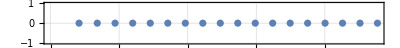

```mathematica
(*Get bessel zeros*)
mm = 2;
mRbh = 2.0;
mRcavity = 65*0.95;
mkmax = 18;

startingZeros = Table[BesselJZero[mm , k]/mRcavity//N, {k,1,mkmax}];
list…of…zeros = List[startingZeros];

(*Plot zeros*)
ComplexListPlot[
startingZeros,
AspectRatio->1/10,
PlotTheme->"Detailed",
ImageSize-> Full]
```

We will change the parameters slowly to get to the final configuration we wish:

```mathematica
(*Alpha parameters*)
alpha0 = 0.00;
alphaf =10.0;
Nalpha = 400;
dalpha = (alphaf-alpha0)/(Nalpha-1);
alpha…list = Table[alpha0 + (i-1)*dalpha,{i,1,Nalpha}];

(*Omega Parameters*)
Omega0 = 0.0;
Omegaf = 0.07475280175130639;
NOmega = 100;
dOmega = (Omegaf - Omega0)/(NOmega-1);
Omega…list = Table[Omega0 + (i-1)*dOmega,{i,1,NOmega}];
```

We begin by increasing the absorption parameter:

```mathematica
(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[i]] (*Alpha*),
0.0 (*Omega*) , 
mm (*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
 list…of…zeros[[-1]]]]
,{i,1,Nalpha}
]
```

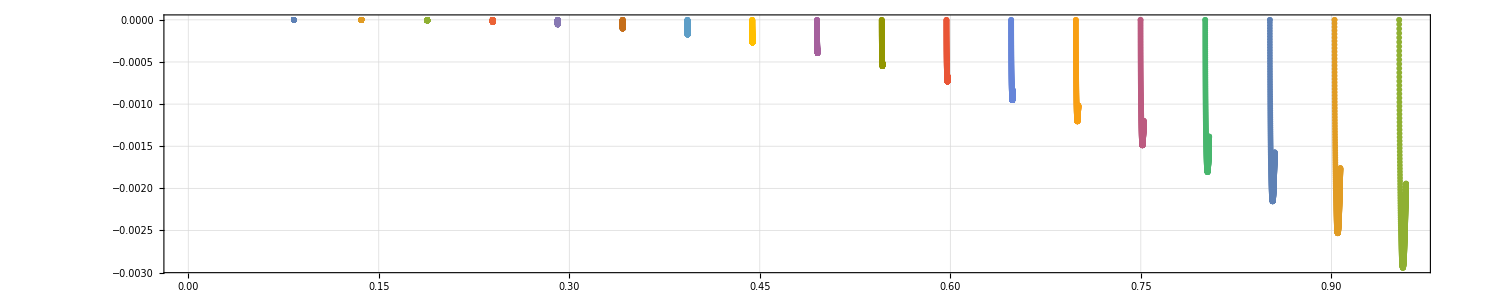

```mathematica
(*Plot Result*)
ComplexListPlot[
Transpose[list…of…zeros],
AspectRatio->1/5,
PlotTheme->"Detailed"]
```

```mathematica
(*Save zeros to files*)
Do[
zero = Transpose[list…of…zeros][[ith]];
outdata = Table[{alpha…list[[j]], Re[list…of…zeros[[j]][[ith]]  ] , Im[list…of…zeros[[j]][[ith]] ] },{j,1,Length[alpha…list]}];
outname = "data/roots_alpha_increase_" <> "_Rbh_" <> ToString[NumberForm[mRbh,{5,2}]]<>"_alpha_"<> ToString[NumberForm[alphaf,{5,2}]] <> "_mode_" <>ToString[NumberForm[mm,{2,0}]] <> "_root_"<> ToString[NumberForm[ith,{2,0}]] <>".txt";
Export[
FileNameJoin[{NotebookDirectory[],outname}], outdata , "Table"];

,{ith,1,mkmax}
]
```

We can now increase the rotation speed to get the frequencies we wish:

```mathematica
(*Get wanted alpha zeros*)
alpha…zeros = list…of…zeros[[-1]];
rotating…list…of…zeros = List[alpha…zeros];

Do[
AppendTo[
rotating…list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[-1]] (*Alpha*),
Omega…list[[i]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
rotating…list…of…zeros[[-1]]]]
,{i,1,NOmega}
]
```

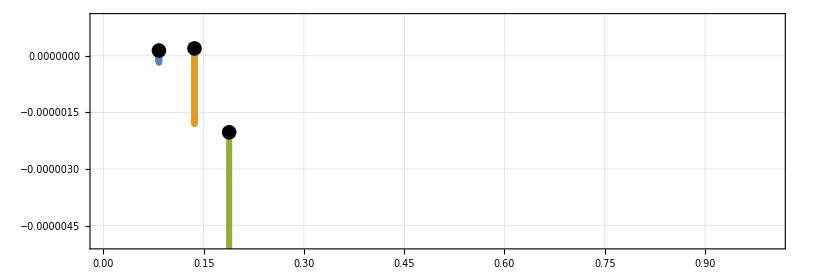

```mathematica
(*Plot Result*)
p1 = ComplexListPlot[
Transpose[rotating…list…of…zeros],
AspectRatio->1/3,
PlotTheme->"Detailed"];

p2 = ComplexListPlot[
rotating…list…of…zeros[[-1]],
AspectRatio->1/3,
PlotTheme->"Detailed", PlotStyle->Black];

Show[p1,p2, PlotRange-> {{0,1},{-0.000005,0.000001}}]
```

```mathematica
(*Save zeros to files*)
Do[
zero = Transpose[list…of…zeros][[ith]];
outdata = Table[{Omega…list[[j]], Re[rotating…list…of…zeros[[j]][[ith]]  ] , Im[rotating…list…of…zeros[[j]][[ith]] ] },{j,1,Length[Omega…list]}];
outname = "data/roots_rotation_increase_" <> "_Rbh_" <> ToString[NumberForm[mRbh,{5,2}]]<>"_alpha_"<> ToString[NumberForm[alphaf,{5,2}]] <> "_mode_" <>ToString[NumberForm[mm,{2,0}]] <> "_root_"<> ToString[NumberForm[ith,{2,0}]] <>".txt";
Export[
FileNameJoin[{NotebookDirectory[],outname}], outdata , "Table"];

,{ith,1,mkmax}
]
```

### Cavity Resonances - One click

```mathematica
(*Get bessel zeros*)
mm = 2;
mRbh = 2.0;
mRcavity = 28.5;
mkmax = 20;

startingZeros = Table[BesselJZero[mm , k]/mRcavity//N, {k,1,mkmax}];
list…of…zeros = List[startingZeros];
```

```mathematica
(*Alpha parameters*)
alpha0 = 0.01;
alphaf =10.0;
Nalpha = 20;
dalpha = (alphaf-alpha0)/(Nalpha-1);
alpha…list = Table[alpha0 + (i-1)*dalpha,{i,1,Nalpha}];

(*Omega Parameters*)
Omega0 = 0.0;
Omegaf = 0.5;
NOmega = 70;
dOmega = (Omegaf - Omega0)/(NOmega-1);
Omega…list = Table[Omega0 + (i-1)*dOmega,{i,1,NOmega}];

(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[i]] (*Alpha*),
0.0 (*Omega*) , 
mm (*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
 list…of…zeros[[-1]]]]
,{i,1,Nalpha}
]

(*Get wanted alpha zeros*)
alpha…zeros = list…of…zeros[[-1]];
rotating…list…of…zeros = List[alpha…zeros];

Do[
AppendTo[
rotating…list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[-1]] (*Alpha*),
Omega…list[[i]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
rotating…list…of…zeros[[-1]]]]
,{i,1,NOmega}
]
```

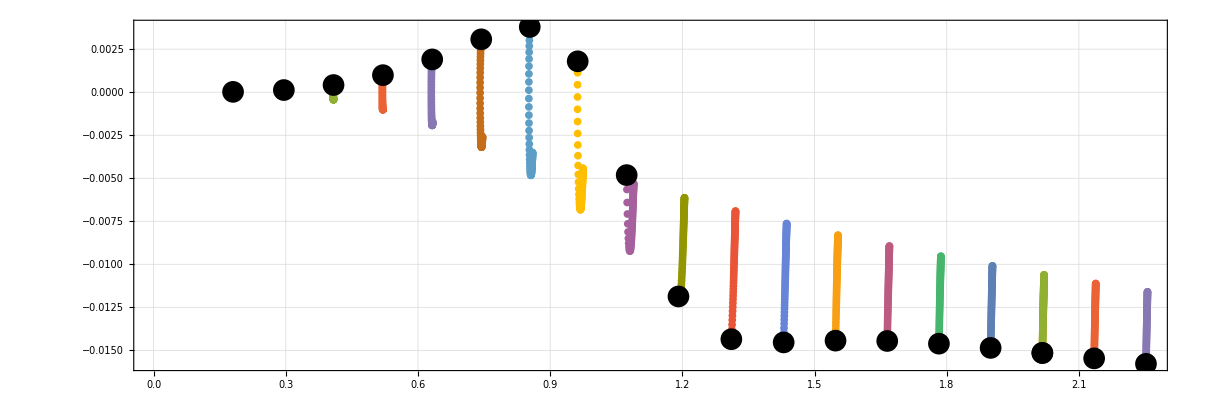

```mathematica
(*Plot Result*)
p1 = ComplexListPlot[
Transpose[rotating…list…of…zeros],
AspectRatio->1/3,
PlotTheme->"Detailed"];

p2 = ComplexListPlot[
rotating…list…of…zeros[[-1]],
AspectRatio->1/3,
PlotTheme->"Detailed", PlotStyle->Black];

Show[p1,p2]
```

### Cavity Resonances - absorption parameter dependence

This section focus on studying the dependence of the fastest growing root on the absorption parameter. We use the previous procedure to find an initial configuration and from the set of roots found, we sweep the absorption parameter.

```mathematica
(*Get bessel zeros*)
mm = 2;
mRbh = 2.0;
mRcavity = 30;
mkmax = 10;

startingZeros = Table[BesselJZero[mm , k]/mRcavity//N, {k,1,mkmax}];
list…of…zeros = List[startingZeros];
```

```mathematica
(*Alpha parameters*)
alpha0 = 0.01;
alphaf =0.02;
Nalpha = 20;
dalpha = (alphaf-alpha0)/(Nalpha-1);
alpha…list = Table[alpha0 + (i-1)*dalpha,{i,1,Nalpha}];

(*Omega Parameters*)
Omega0 = 0.0;
Omegaf = 0.5;
NOmega = 70;
dOmega = (Omegaf - Omega0)/(NOmega-1);
Omega…list = Table[Omega0 + (i-1)*dOmega,{i,1,NOmega}];

(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[i]] (*Alpha*),
0.0 (*Omega*) , 
mm (*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
 list…of…zeros[[-1]]]]
,{i,1,Nalpha}
]

(*Get wanted alpha zeros*)
alpha…zeros = list…of…zeros[[-1]];
rotating…list…of…zeros = List[alpha…zeros];

Do[
AppendTo[
rotating…list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[-1]] (*Alpha*),
Omega…list[[i]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
rotating…list…of…zeros[[-1]]]]
,{i,1,NOmega}
]
```

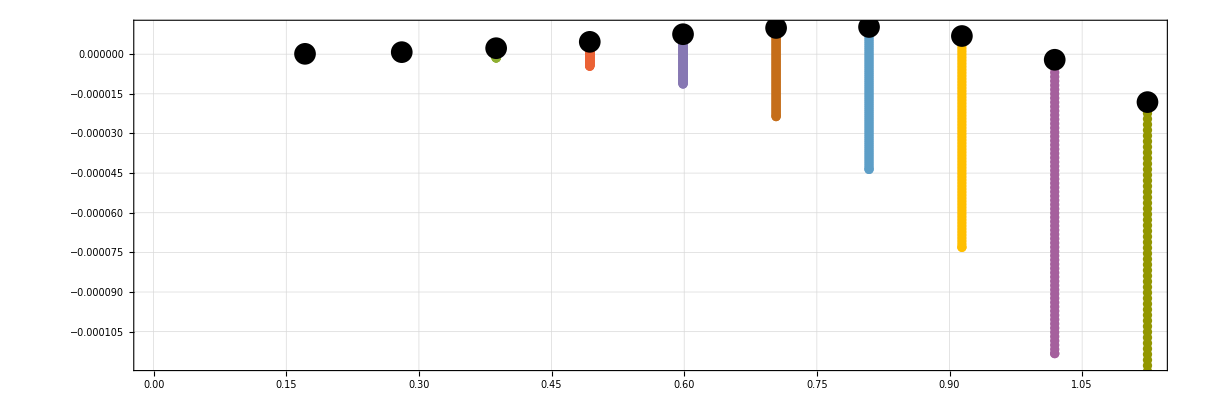

```mathematica
(*Plot Result*)
p1 = ComplexListPlot[
Transpose[rotating…list…of…zeros],
AspectRatio->1/3,
PlotTheme->"Detailed"];

p2 = ComplexListPlot[
rotating…list…of…zeros[[-1]],
AspectRatio->1/3,
PlotTheme->"Detailed", PlotStyle->Black];

Show[p1,p2]
```

With the list of zeros we can sweep the parameters as we wish to see their dependence on the absorption parameter. We begin with a forward search:

```mathematica
(*Alpha parameters for forward search*)
alpha0F = alpha…list[[-1]];
alphafF =50.0;
NalphaF = 100;
dalphaF = (alphafF-alpha0F)/(NalphaF-1);
alpha…list…F = Table[alpha0F + (i-1)*dalphaF,{i,1,NalphaF}];
```

```mathematica
(*Forward Search*)
alphaF…zeros = List[rotating…list…of…zeros[[-1]]];

Do[
AppendTo[
alphaF…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list…F[[i]] (*Alpha*),
Omega…list[[-1]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
alphaF…zeros[[-1]]]]
,{i,1,NalphaF}
]
```

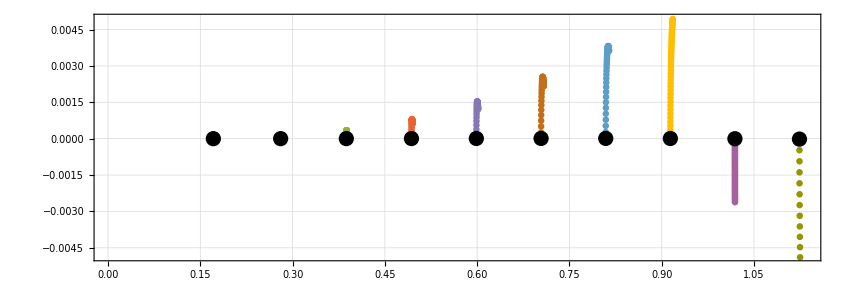

```mathematica
(*Plot Result*)
p3 =ComplexListPlot[
alphaF…zeros [[1]],
AspectRatio->1/3,
PlotTheme->"Detailed", PlotStyle->Black];
p4 = ComplexListPlot[
Transpose[alphaF…zeros[[;;50]]],
AspectRatio->1/3,
PlotTheme->"Detailed"];

Show[p4,p3]
```

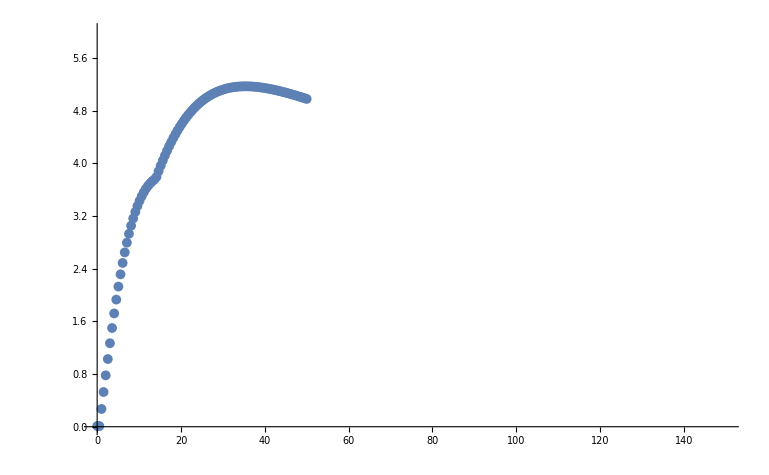

```mathematica
(*Plot maximum amplification growth rate for each absorption parameter value*)
max…amp = List[];
Do[
AppendTo[max…amp, Im[SortBy[alphaF…zeros[[i]],Im][[-1]]] ]
,{i,1,NalphaF}
]

xydata = Transpose[ {alpha…list…F ,max…amp*1000}];
ListPlot[xydata, PlotRange->{{0,150},{0,0.006*1000}}]
```

```mathematica
(*Store values on a file*)
max…amp…Re = List[];
max…amp…Im = List[];

Do[
AppendTo[max…amp…Re, Re[SortBy[alphaF…zeros[[i]],Im][[-1]]] ];
AppendTo[max…amp…Im, Im[SortBy[alphaF…zeros[[i]],Im][[-1]]] ];
,{i,1,NalphaF}
]

xydata = Transpose[ {alpha…list…F ,max…amp…Re ,max…amp…Im  }];

outname2 = "data/maxamp_Omega_" <> ToString[NumberForm[Abs[Omega…list[[-1]] ],{5,2}]]<>"_Rbh_" <> ToString[NumberForm[mRbh,{5,2}]]<>"_Rc_"<> ToString[NumberForm[mRcavity,{5,2}]] <> "_mode_" <>ToString[NumberForm[mm,{2,0}]] <>".txt"

Export[
FileNameJoin[{NotebookDirectory[],outname2}], xydata , "Table"];
```

data/maxamp_Omega_0.50_Rbh_2.00_Rc_30_mode_2.txt

```mathematica
(*Alpha parameters for Backward search*)
alpha0B = alpha…list[[-1]];
alphafB =0.0;
NalphaB = 100;
dalphaB = (alphafB-alpha0B)/(NalphaB-1);
alpha…list…B = Table[alpha0B + (i-1)*dalphaB,{i,1,NalphaB}];
```

```mathematica
(*Backward Search*)
alphaB…zeros = List[rotating…list…of…zeros[[-1]]];

Do[
AppendTo[
alphaB…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list…B[[i]] (*Alpha*),
Omega…list[[-1]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
alphaB…zeros[[-1]]]]
,{i,1,NalphaB}
]
```

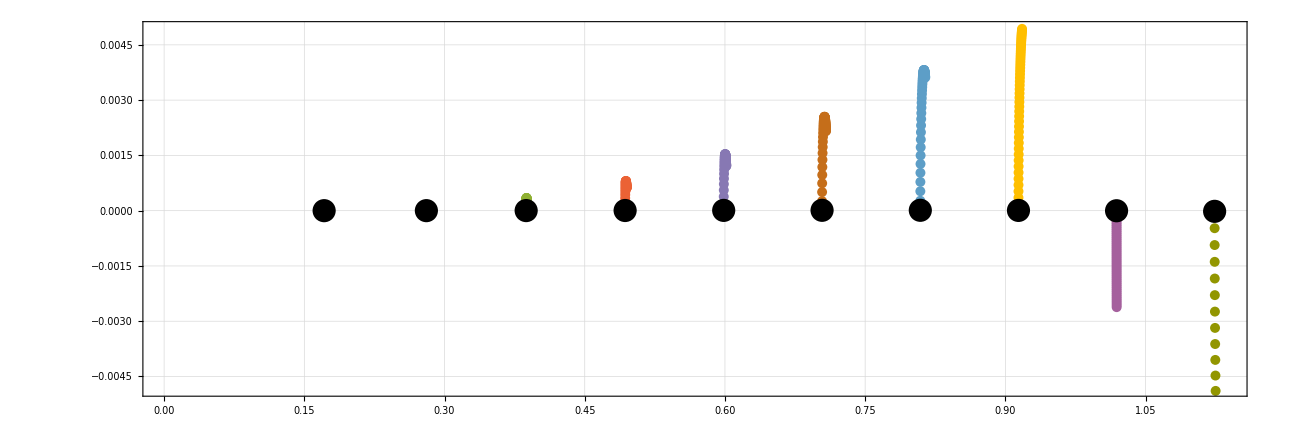

```mathematica
(*Plot Result*)
p3 =ComplexListPlot[
alphaF…zeros [[1]],
AspectRatio->1/3,
PlotTheme->"Detailed", PlotStyle->Black];
p4 = ComplexListPlot[
Transpose[alphaF…zeros[[;;50]]],
AspectRatio->1/3,
PlotTheme->"Detailed"];

Show[p4,p3]
```

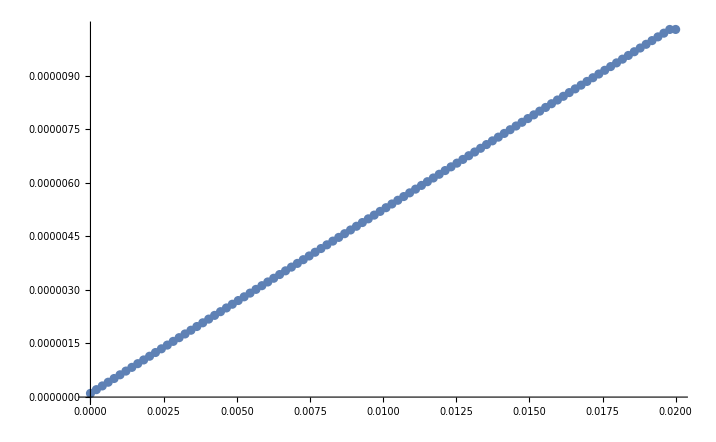

```mathematica
(*Plot maximum amplification growth rate for each absorption parameter value*)
max…amp = List[];

Do[
AppendTo[max…amp, Im[SortBy[alphaB…zeros[[i]],Im][[-1]]] ]
,{i,1,NalphaB}
]
xydata = Transpose[ {alpha…list…B ,max…amp}];
ListPlot[xydata]
```

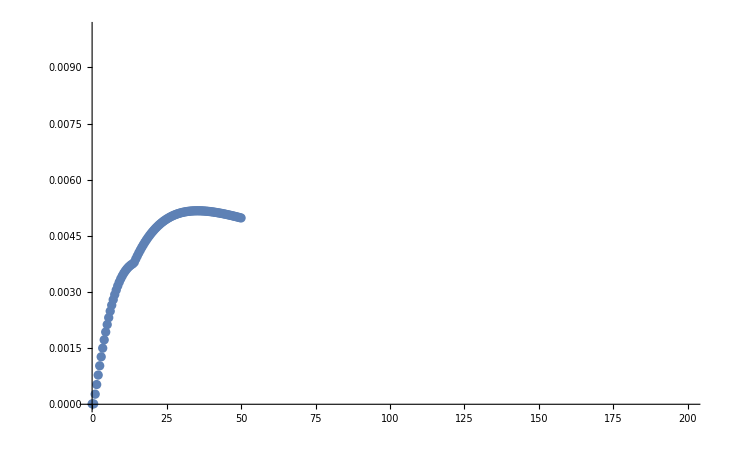

```mathematica
(*Join both searches into a single list*)
max…amp1 = List[];

Do[
AppendTo[max…amp1, Im[SortBy[alphaF…zeros[[i]],Im][[-1]]] ]
,{i,1,NalphaF}
]

xydata = Transpose[ {alpha…list…F ,max…amp1}];

ListPlot[xydata, PlotRange->{{0,200},{0,0.01}}]
```

```mathematica
(*Save all the zeros into a file*)
max…amp…Re = List[];
max…amp…Im = List[];

Do[
AppendTo[max…amp…Re, Re[SortBy[alphaF…zeros[[i]],Im][[-1]]] ];
AppendTo[max…amp…Im, Im[SortBy[alphaF…zeros[[i]],Im][[-1]]] ];
,{i,1,NalphaF}
]

xydata = Transpose[ {alpha…list…F ,max…amp…Re ,max…amp…Im  }];

outname2 = "data/maxamp_Omega_" <> ToString[NumberForm[Abs[Omega…list[[-1]] ],{5,2}]]<>"_Rbh_" <> ToString[NumberForm[mRbh,{5,2}]]<>"_Rc_"<> ToString[NumberForm[mRcavity,{5,2}]] <> "_mode_" <>ToString[NumberForm[mm,{2,0}]] <>".txt"

Export[
FileNameJoin[{NotebookDirectory[],outname2}], xydata , "Table"];
```

data/maxamp_Omega_0.50_Rbh_2.00_Rc_80_mode_1.txt

### Cavity Resonances - Cavity size dependence

The firs blocks are exactly the same as the ones presented in the “Method Explanation” tab.

```mathematica
(*Get bessel zeros*)
mm = 3;
mRbh = 2.0;
mRcavity = 10.5;
mkmax = 5;

startingZeros = Table[BesselJZero[mm , k]/mRcavity//N, {k,1,mkmax}];
list…of…zeros = List[startingZeros];
```

```mathematica
(*Alpha parameters*)
alpha0 = 0.1;
alphaf =1.0;
Nalpha = 50;
dalpha = (alphaf-alpha0)/(Nalpha-1);
alpha…list = Table[alpha0 + (i-1)*dalpha,{i,1,Nalpha}];

(*Omega Parameters*)
Omega0 = 0.0;
Omegaf = 0.5;
NOmega = 70;
dOmega = (Omegaf - Omega0)/(NOmega-1);
Omega…list = Table[Omega0 + (i-1)*dOmega,{i,1,NOmega}];

(*Search for sucessive zeros with different alpha parameters*)
Do[
AppendTo[
list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[i]] (*Alpha*),
0.0 (*Omega*) , 
mm (*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
 list…of…zeros[[-1]]]]
,{i,1,Nalpha}
]

(*Get wanted alpha zeros*)
alpha…zeros = list…of…zeros[[-1]];
rotating…list…of…zeros = List[alpha…zeros];

Do[
AppendTo[
rotating…list…of…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[-1]] (*Alpha*),
Omega…list[[i]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
mRcavity(* Cavity Radius *)],
rotating…list…of…zeros[[-1]]]]
,{i,1,NOmega}
]
```

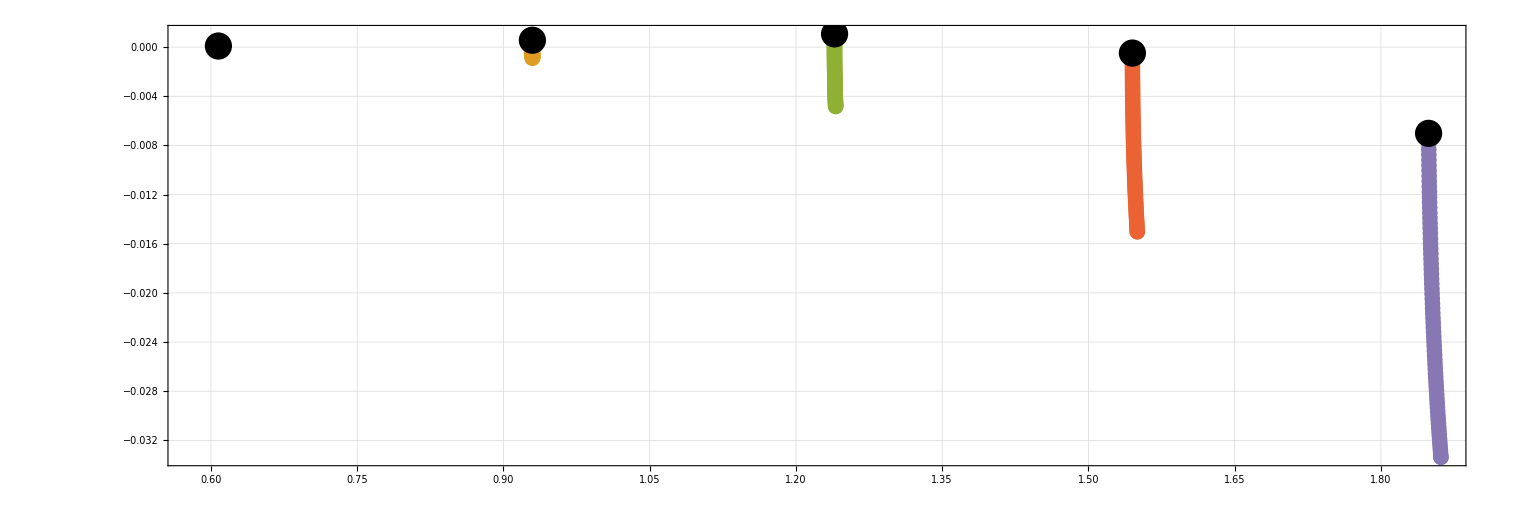

```mathematica
(*Plot Result*)
p1 = ComplexListPlot[
Transpose[rotating…list…of…zeros],
AspectRatio->1/3,
PlotTheme->"Detailed"];

p2 = ComplexListPlot[
rotating…list…of…zeros[[-1]],
AspectRatio->1/3,
PlotTheme->"Detailed", PlotStyle->Black];

Show[p1,p2]
```

With the list of zeros we can sweep the parameters as we wish to see their dependence on the absorption parameter

```mathematica
(*Alpha parameters for forward search*)
Rc0F = mRcavity;
RcfF =2.0;
NRcF = 200;
dRcF = (RcfF-Rc0F)/(NRcF-1);
Rc…list…F = Table[Rc0F + (i-1)*dRcF,{i,1,NRcF}];
```

```mathematica
(*Forward Search*)
RcF…zeros = List[rotating…list…of…zeros[[-1]]];

Do[
AppendTo[
RcF…zeros, 
get…zero…list…from[
 Gw[w,
alpha…list[[-1]] (*Alpha*),
Omega…list[[-1]](*Omega*) , 
mm(*Azimuthal mode *),
mRbh (*BH radius*),
Rc…list…F[[i]](* Cavity Radius *)],
RcF…zeros[[-1]]]]
,{i,1,NRcF}
]
```

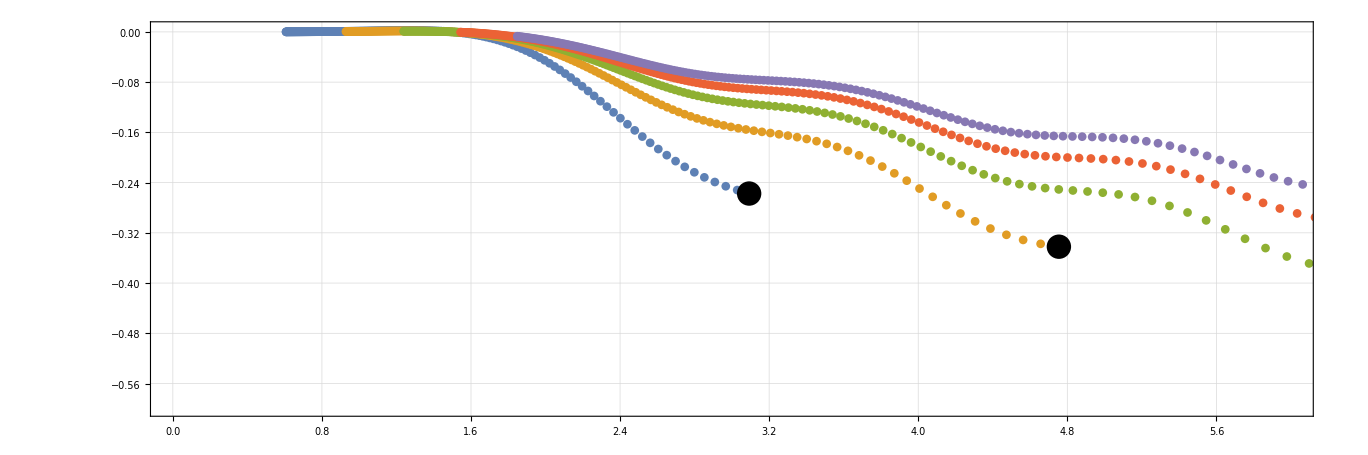

```mathematica
(*Plot Result*)
p3 =ComplexListPlot[
RcF…zeros [[200]],
AspectRatio->1/3,
PlotRange->{{0,2},{-1.5,0.1}},
PlotTheme->"Detailed", PlotStyle->Black]
p4 = ComplexListPlot[
Transpose[RcF…zeros[[;;200]]],
AspectRatio->1/3,
PlotRange->{{0,6},{-0.6,0.004}},
PlotTheme->"Detailed"];

Show[p4,p3]
```

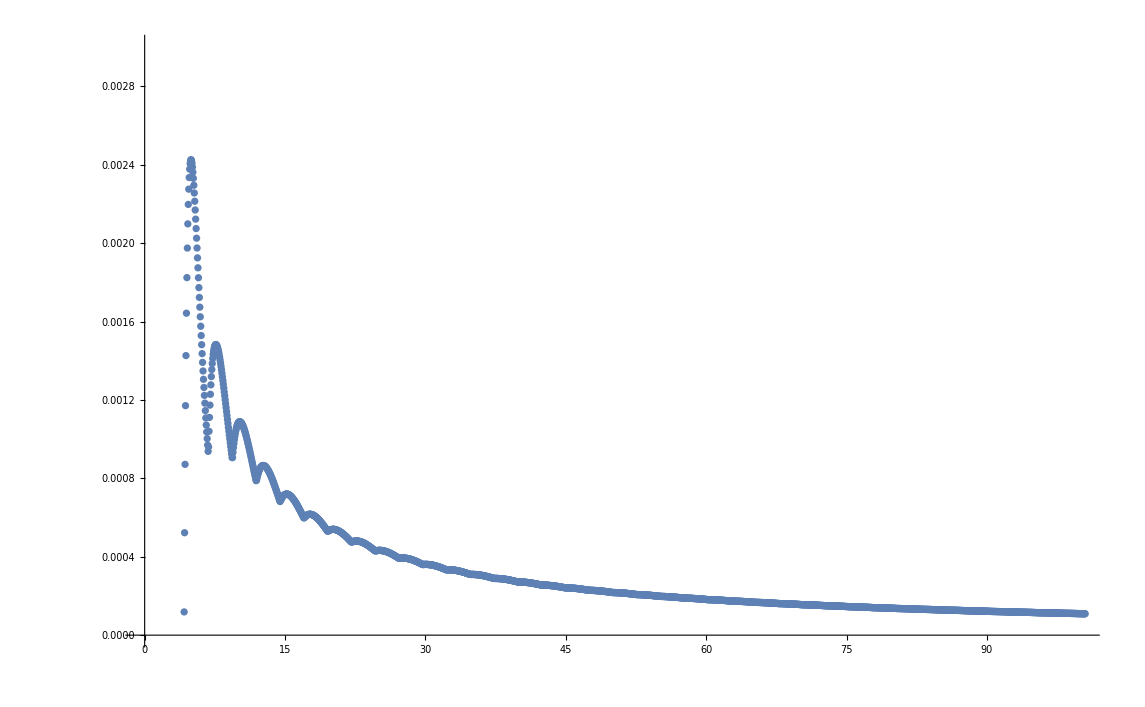

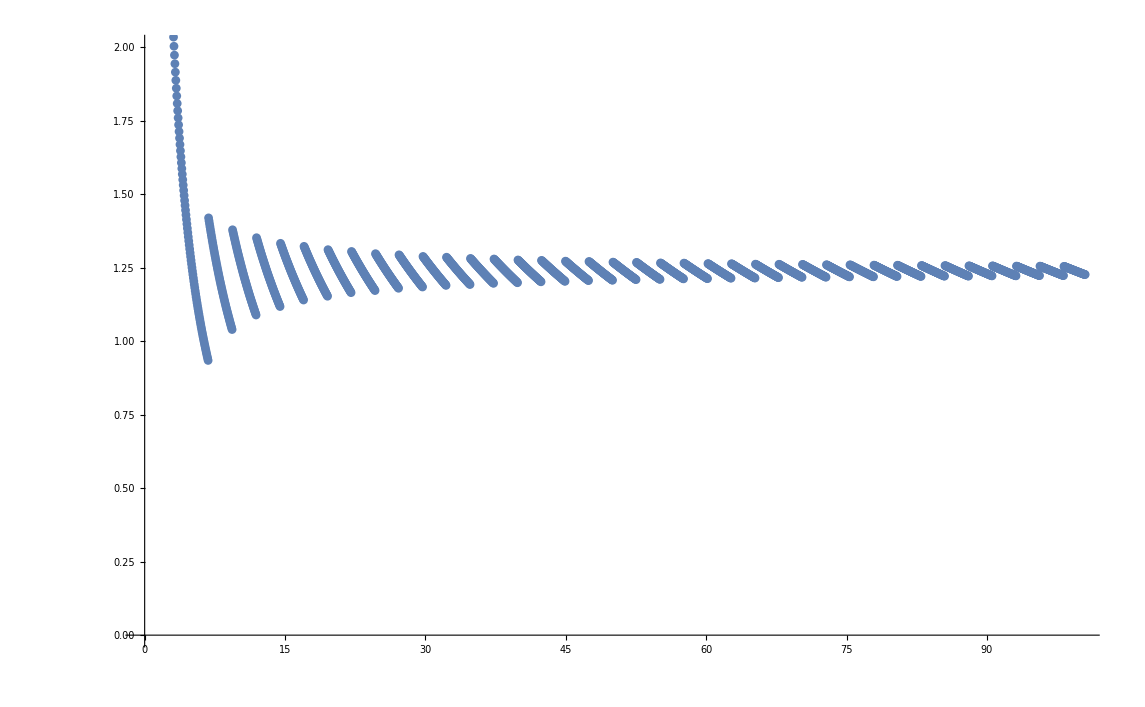

```mathematica
(*For each value of alpha, find the maximum*)
max…amp…Re = List[];
max…amp…Im = List[];
Do[
AppendTo[max…amp…Re, Re[SortBy[RcF…zeros[[i]],Im][[-1]]] ]
,{i,1,NRcF}
]
Do[
AppendTo[max…amp…Im, Im[SortBy[RcF…zeros[[i]],Im][[-1]]] ]
,{i,1,NRcF}
]

Redata = Transpose[ {Rc…list…F ,max…amp…Re}];
Imdata = Transpose[ {Rc…list…F ,max…amp…Im}];

ListPlot[Imdata, PlotRange->{{0,100},{0,0.003}}]
ListPlot[Redata, PlotRange->{{0,100},{0,2}}]
```

```mathematica
(*For each value of alpha, find the maximum*)
max…amp…Re = List[];
max…amp…Im = List[];

Do[
AppendTo[max…amp…Re, Re[SortBy[RcF…zeros[[i]],Im][[-1]]] ];
AppendTo[max…amp…Im, Im[SortBy[RcF…zeros[[i]],Im][[-1]]] ];
,{i,1,NRcF}
]

xydata = Transpose[ {Rc…list…F ,max…amp…Re ,max…amp…Im  }];

outname2 = "data/Cavity_radius_study_Omega_" <> ToString[NumberForm[Abs[Omega…list[[-1]] ],{5,2}]]<>"_Rbh_" <> ToString[NumberForm[mRbh,{5,2}]]<>"_alpha_"<> ToString[NumberForm[alphaf,{5,2}]] <> "_mode_" <>ToString[NumberForm[mm,{2,0}]] <>".txt"

Export[
FileNameJoin[{NotebookDirectory[],outname2}], xydata , "Table"];
```

data/Cavity_radius_study_Omega_0.50_Rbh_2.00_alpha_1.00_mode_3.txt